## Уровень заряда батареи

Анализ лога заряда батареи

Tue 20 Sep 2016 01:18:39

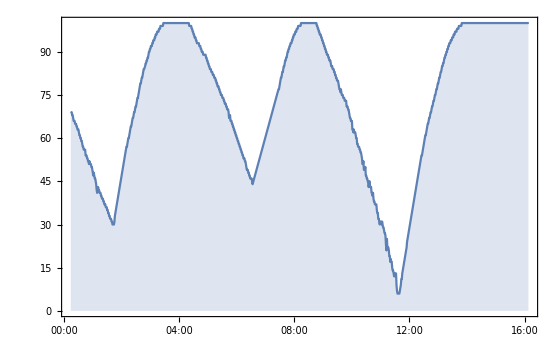

```mathematica
showLog[]:=
Module[{d},
Print[DateString[]];d=Import["/Users/vadimivlev/shell-scripts/battery-level-log.csv"];
DateListPlot[d,Filling->Axis, PlotMarkers->{Automatic,1}]
]
showLog[]
```

#### Второй вариант

```mathematica
log={};
level:=ReadList["!pmset -g ps | egrep -o '(\\d+)%' | egrep -o '\\d+'",Number]⟦1⟧;
takeLevel:=AppendTo[log,{Now, level}]
```

```mathematica
takeNLevels[n_]:=( log={};RunScheduledTask[AppendTo[log,{Now, level}],{60,n}];)
Row[{
Button["Measure 50 times", takeNLevels[1000]],
Button["Stop",RemoveScheduledTask[ScheduledTasks[]]]
}]
```

Measure 50 timesStop

```mathematica
Dynamic[DateListPlot[log,Filling->Bottom, PlotMarkers->{Automatic,1}]]
```